```mathematica
(*równania liniowe*)
```

```mathematica
Clear[a , b , c , eq1 , sol1 , m];
```

```mathematica
eq1 = {2 a + b + 3 c == 5 , a - b == 10 , b - 10 c == 4};
```

```mathematica
And@@eq1
```

2 a+b+3 c==5&&a-b==10&&b-10 c==4

```mathematica
Solve[%]//N
```

{{a→5.81818,b→-4.18182,c→-0.818182}}

```mathematica
NSolve[eq1 , {a , b , c}]
```

{{a→5.81818,b→-4.18182,c→-0.818182}}

```mathematica
sol1 = Solve[eq1 , {a , b , c}]
```

{{a→64/11,b→-46/11,c→-9/11}}

```mathematica
sol1[[1]]
```

{a→64/11,b→-46/11,c→-9/11}

```mathematica
a/.sol1[[1]]
```

64/11

```mathematica
eq1
```

{2 a+b+3 c==5,a-b==10,b-10 c==4}

```mathematica
m = {{2 , 1 , 3} , {1 , -1 , 0} , {0 , 1 , -10}};
```

```mathematica
v = {5 , 10 , 4};
```

```mathematica
m.{a , b , c} == v
```

{2 a+b+3 c,a-b,b-10 c}=={5,10,4}

```mathematica
Solve[m.{a , b , c} == v , {a , b , c}]
```

{{a→64/11,b→-46/11,c→-9/11}}

```mathematica
Table[Sum[m[[r , k]] {a , b , c}[[k]] , {k , 1 , 3}] , {r , 1 , 3}]
```

{2 a+b+3 c,a-b,b-10 c}

```mathematica
m.{a , b , c}
```

{2 a+b+3 c,a-b,b-10 c}

```mathematica
N[1]
```

1.

```mathematica
LinearSolve[m//N , v//N]
```

{5.81818,-4.18182,-0.818182}

```mathematica
(*Znajdowanie miejsc zerowych*)
```

```mathematica
Clear[y];
```

```mathematica
y[x_] := x^2 - 3;
```

```mathematica
(*y[x] == 0*)
```

```mathematica
FindRoot[y[x] , {x , 1.}]
```

{x→1.73205}

```mathematica
FindRoot[y[x] , {x , -1.}]
```

{x→-1.73205}

```mathematica
(*równania różniczkowe*)
```

```mathematica
Clear[f , sol2]
```

```mathematica
f''[x]//FullForm
```

Derivative[2][f][x]

```mathematica
D[f[x] , {x , 2}]
```

f''[x]

```mathematica
D[u[x , y] , y]
```

u^(0,1)[x,y]

```mathematica
%//FullForm
```

Derivative[0,1][u][x,y]

```mathematica
Derivative[0 , 1][u]
```

u^(0,1)

```mathematica
%[x , y]
```

u^(0,1)[x,y]

```mathematica
DSolve[f''[t] == -f[t], f[t] , t]
```

{{f[t]→C[1] Cos[t]+C[2] Sin[t]}}

```mathematica
DSolve[f''[t] == -f[t]&&f[0] == 0, f[t] , t]
```

{{f[t]→C[2] Sin[t]}}

```mathematica
DSolve[{f''[t] == -f[t],f[0] == 0 , f'[0] == 1}, f[t] , t]
```

{{f[t]→Sin[t]}}

```mathematica
DSolve[{f''[t] == -f[t],f[0] == 0 , f'[0] == 1}, f , t]
```

{{f→Function[{t},Sin[t]]}}

```mathematica
NDSolve[{f''[t] == -f[t],f[0] == 0 , f'[0] == 1}, f[t] , {t , 0 , 10}]
```

{{f[t]→InterpolatingFunction[…][t]}}

```mathematica
sol2 = NDSolve[{f''[t] == -f[t],f[0] == 0 , f'[0] == 1}, f , {t , 0 , 10}]
```

{{f→InterpolatingFunction[…]}}

```mathematica
f/.sol2[[1]]
```

InterpolatingFunction[…]

```mathematica
(f/.sol2[[1]])[1]
```

0.841471

```mathematica
fsol = f/.sol2[[1]];
```

```mathematica
fsol[12]
```

InterpolatingFunction::dmval: Input value {12} lies outside the range of data in the interpolating function. Extrapolation will be used.

-0.605417

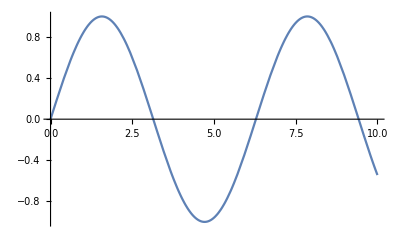

```mathematica
Plot[fsol[t] , {t , 0 , 10}]
```

InterpolatingFunction::dmval: Input value {-1.99971} lies outside the range of data in the interpolating function. Extrapolation will be used.

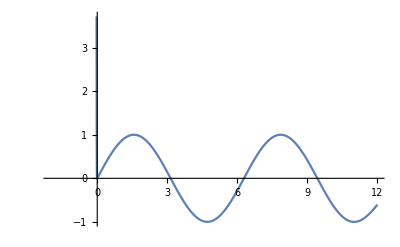

```mathematica
Plot[fsol[t] , {t , -2 , 12}]
```

InterpolatingFunction::dmval: Input value {-1.99971} lies outside the range of data in the interpolating function. Extrapolation will be used.

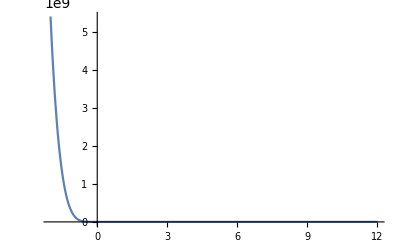

```mathematica
Plot[fsol[t] , {t , -2 , 12} , PlotRange->All]
```

```mathematica
(*całkowanie*)
```

```mathematica
Clear[kolo,p];
```

```mathematica
kolo[x_ , y_]:= If[x^2+y^2<= 1 , 1 , 0];
```

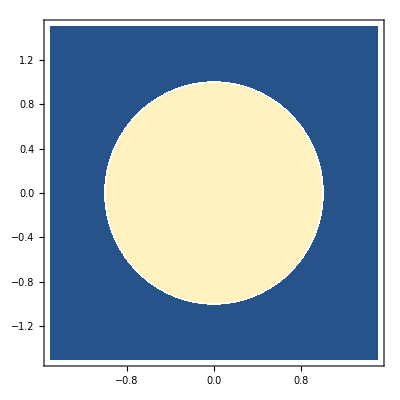

```mathematica
DensityPlot[kolo[x , y], {x , -1.5 , 1.5} , {y , -1.5 , 1.5}]
```

```mathematica
(*ESC + inf + ESC*)
```

```mathematica
Integrate[kolo[x , y] , {x , -∞ , +∞} , {y , -∞ ,+∞}]
```

π

```mathematica
NIntegrate[kolo[x , y] , {x , -2 , 2} , {y , -2 ,2}]
```

3.14159

```mathematica
(*liczenie różniczek*)
```

```mathematica
p[x_]:= Exp[x]+Sin[x];
```

```mathematica
dp = Derivative[1][p]
```

ⅇ^#1+Cos[#1]&

```mathematica
(#^2)&[10]
```

100

```mathematica
dp[x]
```

ⅇ^x+Cos[x]

```mathematica
p'[x]
```

ⅇ^x+Cos[x]

```mathematica
D[p[x] , x]
```

ⅇ^x+Cos[x]

```mathematica
Integrate[%  , x]
```

ⅇ^x+Sin[x]

```mathematica
(*upraszczanie wyrażeń*)
```

```mathematica
Hold[FullForm[(x|y|z)∈Reals&&x > 0]]
```

Hold[And[Element[Alternatives[x,y,z],Reals],Greater[x,0]]]

```mathematica
(*ESC + el + ESC*)
```

```mathematica
$Assumptions = (x|y|z)∈Reals&&x > 0;
```

```mathematica
FullSimplify[x>0]
```

True

```mathematica
FullSimplify[Im[x + y + z] == 0]
```

True

```mathematica
Exp[ⅈ ϕ]//ComplexExpand
```

Cos[ϕ]+ⅈ Sin[ϕ]

```mathematica
(*Simplify*)
```

```mathematica
(*FullSimplify[... , TimeConstraint->1]*)
```

```mathematica
(*Expand , ExpandAll*)
```